## 多层神经网络

```mathematica
σ[x_]:=1/(1+Power[ⅇ, -x]);
dσ[x_]:=σ[x](1-σ[x]);
SetAttributes[dσ,Listable];
SetAttributes[σ,Listable];
```

```mathematica
(*要求X是m×r的矩阵, Y是p×r的矩阵, n是隐藏层神经元的个数, l-1是隐藏层的层数*)
MBPNN[X__,Y__,n_,l_]:=Module[{r=0,m=0,p=0,Error=100,err={},W={},b={},er={},a={},z={},δ={},η=0.5,iterMax=10000},
{m,r}=Dimensions[X];{p,r}=Dimensions[Y];
AppendTo[W,RandomReal[{-1,1},{n,m}]];
(AppendTo[W,RandomReal[{-1,1},{n,n}]])&/@Range[2,l-1];
AppendTo[W,RandomReal[{-1,1},{p,n}]];
(AppendTo[b,RandomReal[{-1,1},{n,1}]])&/@Range[1,l-1];
AppendTo[b,RandomReal[{-1,1},{p,1}]];
(*********************************************************************)
er={Table[1,{i,r}]};

While[Error>0.001&&iterMax>0,
iterMax--;
AppendTo[z,W[[1]].X+b[[1]].er];
(AppendTo[a,σ[z[[#]]]];AppendTo[z,W[[#+1]].a[[#]]+b[[#+1]].er])&/@Range[1,l-1];
AppendTo[a,σ[z[[l]]]];
Error=1/2 Norm[a[[l]]-Y,"Frobenius"]^2;
AppendTo[err,Error];
PrependTo[δ,(a[[l]]-Y)*dσ[z[[l]]]];
PrependTo[δ,(Transpose[W[[#+1]]].δ[[1]])*dσ[z[[#]]]]&/@Table[i,{i,l-1,1,-1}];
(W[[#]]=W[[#]]-η δ[[#]].Transpose[a[[#-1]]])&/@Range[2,l];
W[[1]]=W[[1]]-η δ[[1]].Transpose[X];
(b[[#]]=b[[#]]-η δ[[#]].Transpose[er])&/@Range[l];
a={};z={};δ={};
];
{W,b,err}
]
```

```mathematica
predict[W__,b__,X__]:=Module[{z={},a={},l=Length[W],r=Length[X[[1]]],er={}},
er={Table[1,{i,r}]};
AppendTo[z,W[[1]].X+b[[1]].er];
(AppendTo[a,σ[z[[#]]]];AppendTo[z,W[[#+1]].a[[#]]+b[[#+1]].er])&/@Range[1,l-1];
AppendTo[a,σ[z[[l]]]];
a[[l]]
]
```

### 经过batch的神经网络训练

{{1.04698,1.88949,3.05878},{6.99932,8.15313,8.6527}}

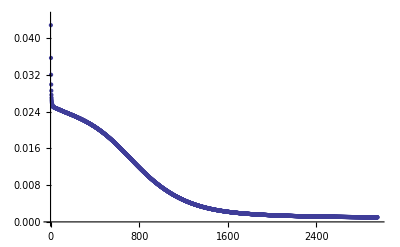

```mathematica
X={{1,2,3},{4,5,6},{7,8,9},{10,11,12}};
Y={{1,2,3},{7,8,9}}/9;
res=MBPNN[X,Y,8,3];
predict[res[[1]],res[[2]],X]*9
ListPlot[res[[3]]]
```

## debug area

```mathematica
Xs={{1,2,3},{4,5,6},{7,8,9},{10,11,12}};
Ys={{1,2,3},{7,8,9}}/9;
```

```mathematica
x1=(t=RandomReal[{-π,π}];x=8Cos[t]+Sin[RandomReal[{-π,π}]];y=8Sin[t]+Sin[RandomReal[{-π,π}]];{x,y,x^2,y^2,x y})&/@Range[100];
x2=(t=RandomReal[{-π,π}];x=4Cos[t]+Sin[RandomReal[{-π,π}]];y=4Sin[t]+Sin[RandomReal[{-π,π}]];{x,y,x^2,y^2,x y})&/@Range[100];
y1=({Boole[RandomReal[]>0]})&/@Range[100];
y2=({Boole[RandomReal[]<0]})&/@Range[100];
Xs=Transpose[Join[x1,x2]];
Ys=Transpose[Join[y1,y2]];
```

```mathematica
batch=10;
n=4;l=3;
{r=0,m=0,p=0,Error=100,W={},b={},er={},a={},z={},δ={},η=0.03};
{m,r}=Dimensions[Xs];{p,r}=Dimensions[Ys];
AppendTo[W,RandomReal[{-1,1},{n,m}]];
(AppendTo[W,RandomReal[{-1,1},{n,n}]])&/@Range[2,l-1];
AppendTo[W,RandomReal[{-1,1},{p,n}]];
(AppendTo[b,RandomReal[{-1,1},{n,1}]])&/@Range[1,l-1];
AppendTo[b,RandomReal[{-1,1},{p,1}]];
(*********************************************************************)
er={Table[1,{i,batch}]};
```

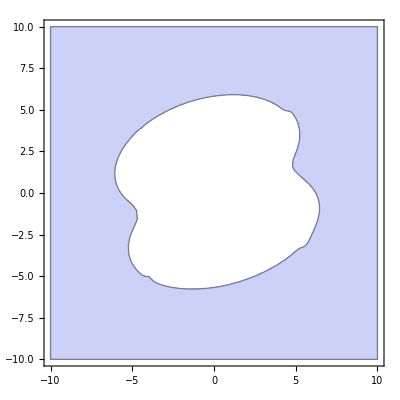

```mathematica
iterMax=10000;
err={};
minerr=Error;
Dynamic[{(MatrixPlot[#])&/@W,iterMax,minerr}]
Dynamic[RegionPlot[First@First@predict[minW,minb,{{xx},{yy},{xx^2},{yy^2},{xx yy}}]>0.5,{xx,-10,10},{yy,-10,10}]]
While[Error>0.000001&&iterMax>0,
iterMax--;
sample=RandomSample[Range[r],batch];
X=Xs[[All,sample]];
Y=Ys[[All,sample]];
AppendTo[z,W[[1]].X+b[[1]].er];
(AppendTo[a,σ[z[[#]]]];AppendTo[z,W[[#+1]].a[[#]]+b[[#+1]].er])&/@Range[1,l-1];
AppendTo[a,σ[z[[l]]]];
Error=1/2 Norm[a[[l]]-Y,"Frobenius"]^2;
If[minerr>Error,minerr=Error;AppendTo[err,Error];minW=W;minb=b];
PrependTo[δ,(a[[l]]-Y)*dσ[z[[l]]]];
PrependTo[δ,(Transpose[W[[#+1]]].δ[[1]])*dσ[z[[#]]]]&/@Table[i,{i,l-1,1,-1}];
(W[[#]]=W[[#]]-η δ[[#]].Transpose[a[[#-1]]])&/@Range[2,l];
W[[1]]=W[[1]]-η δ[[1]].Transpose[X];
(b[[#]]=b[[#]]-η δ[[#]].Transpose[er])&/@Range[l];
a={};z={};δ={};
];
RegionPlot[First@First@predict[W,b,{{xx},{yy},{xx^2},{yy^2},{xx yy}}]>0.5,{xx,-10,10},{yy,-10,10}]
```

200

200

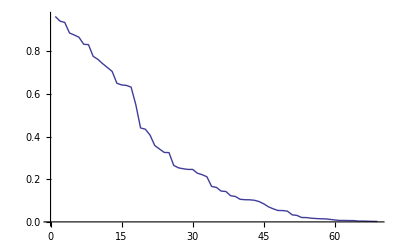

```mathematica
Length[Select[Transpose[{Boole[#>0.5]&/@predict[W,b,Xs][[1]],Ys[[1]]}],#[[1]]==#[[2]]&]]
Length[Select[Transpose[{Boole[#>0.5]&/@predict[minW,minb,Xs][[1]],Ys[[1]]}],#[[1]]==#[[2]]&]]
ListLinePlot[err]
```

```mathematica
alldata=SplitBy[SortBy[Join[Flatten[#]&/@Transpose[{x1[[All,1;;2]],y1}],Flatten[#]&/@Transpose[{x2[[All,1;;2]],y2}]],#[[3]]&],#[[3]]&];
```

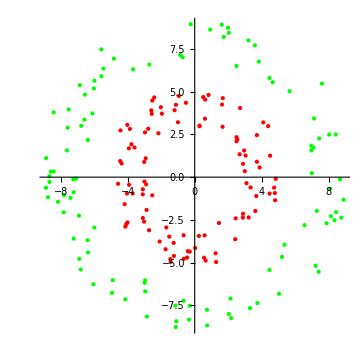

```mathematica
ListPlot[alldata[[All,All,1;;2]],AspectRatio->1,PlotStyle->{Red,Green}]
```